```mathematica
(*This is the graph of B/I*)

dataset = Import["/Volumes/GoogleDrive/My Drive/TexasA&M/4-Semester/327_328-PHYS/Labs/7_Lab/t1.csv"];
```

```mathematica
TableForm[dataset] (*Display Table*)
```

Current (A) | Magnetic Field (uT) | Predicted Magnetic Field (uT) | Residuals | Uncertainty (uT)
1.97 | 1517.41 | 1515.19 | 2.22415 | 0.2
1.88 | 1446.45 | 1445.29 | 1.1613 | 0.2
1.75 | 1335.76 | 1344.33 | -8.56615 | 0.2
1.63 | 1253.54 | 1251.13 | 2.41005 | 0.2
1.54 | 1185.59 | 1181.23 | 4.3572 | 0.2
1.4 | 1079.97 | 1072.5 | 7.4661 | 0.2
1.29 | 973.52 | 987.074 | -13.5541 | 0.2
1.07 | 820.71 | 816.214 | 4.49565 | 0.2

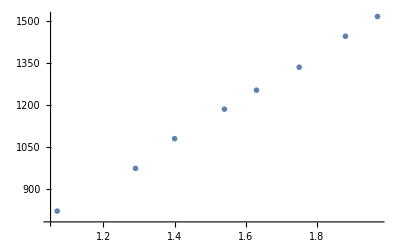

```mathematica
col1 = dataset[[All, 1]][[2 ;; 9]]; (*Current*)
col2 = dataset[[All, 2]][[2 ;; 9]]; (*Magnetic Field*)
col3 = dataset[[All, 3]][[2 ;; 9]]; (*Predicted*)
col4 = dataset[[All, 4]][[2 ;; 9]]; (*Residuals*)
col5 = dataset[[All, 5]][[2 ;; 9]]; (*Uncertainty*)

(*Pair Data*)
dataInterop = {col1, col2};
dataBundle = Transpose[dataInterop];


TableForm[dataBundle];  (*Display Table*)
ListPlot[dataBundle,PlotMarkers->{"o",Large}] (*Graph Data*)
```

```mathematica
lm = LinearModelFit[dataBundle, x, x];
Normal@lm (*Print out line of least squares fit*)
```

-14.7851+776.635 x

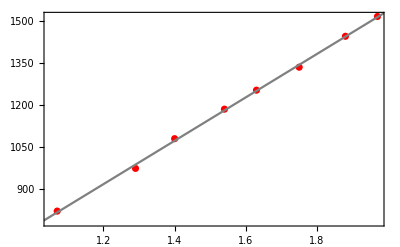
-Graphics-Magnetic Field Strength (B)Current (A)

```mathematica
l9 = Labeled[
Show[
ListPlot[dataBundle, PlotStyle->Red],
Plot[lm[x],{x,0,2000}, PlotStyle->Gray], (*Take note of bounds*)
Frame->True], 
{"Magnetic Field Strength (B)", "Current (A)"},
{Left, Bottom},
RotateLabel->True
]
```

```mathematica
(*-------------------------------------------------------------------------------------------*)
(*-------------------------------------------------------------------------------------------*)
(*-------------------------------------------------------------------------------------------*)
(*-------------------------------------------------------------------------------------------*)
```

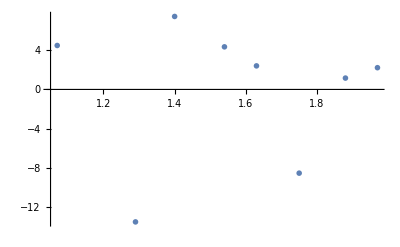

```mathematica
(*Pair Data*)
dataInteropResidual = {col1, col4}; (*current, residuals*)
dataBundleResidual = Transpose[dataInteropResidual];

(*Graph Data*)
ListPlot[dataBundleResidual,PlotMarkers->{"o",Large}]
```

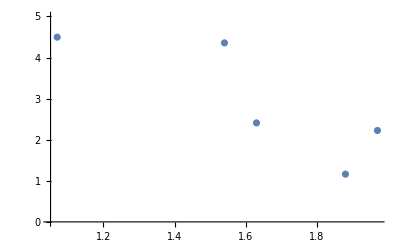
-Graphics-Magnetic Field Strength Residuals (B)Current (A)

```mathematica
(*Pair Data with Uncertainty*)
dataWUncertainty = {col1, col4, col5}; (*current, residuals, uncertainty*)
dataBundleWUncertainty = Transpose[dataWUncertainty];


(*Error Bars work, they are just really small*)
Needs["ErrorBarPlots`"]
l0 = Labeled[
	Show[
	ListPlot[dataBundleResidual, PlotRange->{0, 5}],     (*Note the Range*)
	Plot[lm[x],{x,0,2}],
	ErrorListPlot[dataBundleWUncertainty,PlotStyle->Gray]
   ],
{"Magnetic Field Strength Residuals (B)", "Current (A)"},
{Left, Bottom},
RotateLabel->True
]
```

```mathematica
Export[NotebookDirectory[]<>"graph_71.png", l9, ImageResolution-> 200]
Export[NotebookDirectory[]<>"graph_residual71.png", l0, ImageResolution-> 200]
```

/Volumes/GoogleDrive/My Drive/TexasA&M/4-Semester/327_328-PHYS/Labs/7_Lab/graph_71.png

/Volumes/GoogleDrive/My Drive/TexasA&M/4-Semester/327_328-PHYS/Labs/7_Lab/graph_residual71.png